```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

### Define required functions

```mathematica
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];

ImV[r_,mD_,α_,σ_,T_]:=ImVc[r,mD,α,T]+ImVs[r,mD,σ,T];

ImVsb[r_,mD_,α_,σ_,T_,rsb_]:=If[r<rsb,ImV[r,mD,α,σ,T],ImV[rsb,mD,α,σ,T]];

ReV[r_,m_,α_,σ_,c_]:=c-α m-α Exp[-m r]/r+(2 σ)/m-(ⅇ^(-m r) (2+m r) σ)/m;

ReVsb[r_,m_,α_,σ_,c_]:=If[ReV[r,m,α,σ,c]<ReVsbVac,ReV[r,m,α,σ,c],ReVsbVac];

ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
```

```mathematica
mDcalmu[T_,μ_,c_,d_]:=Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)μ^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ];
```

```mathematica
rsbvac=r/.FindRoot[ReVm0[r,αcont[[1]],σcont[[1]],ccont[[1]]]==ReVsbVac,{r,10}]
```

6.14511

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s-wave without string breaking

```mathematica
ImV[r_,mD_,α_,σ_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4])+1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

```mathematica
ImVc[1000000,mDcalmu[0.155,0,kfinal[[1]],kfinal[[2]]],αcont[[1]],0.155]
```

0.079508

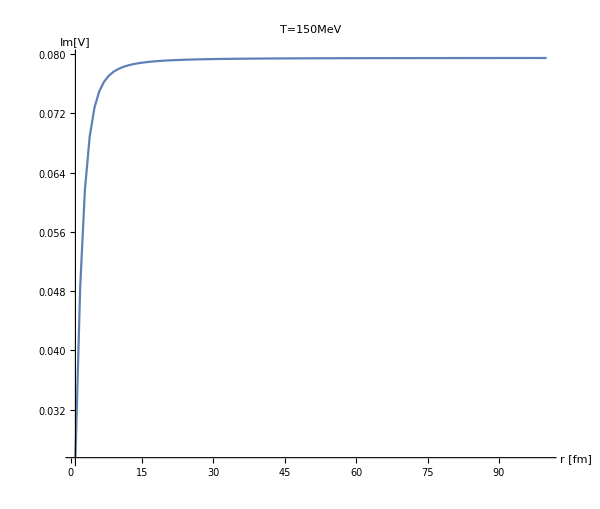

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVc[r/0.197,mD,αcont[[1]],0.155],{r,1,100,1},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
Series[1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4],{r,∞,10}]//FullSimplify
```

ⅇ^(-ⅈ √(-mD^2) r) ((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2))+O[1/r]^7)+ⅇ^(ⅈ √(-mD^2) r) ((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3+O[1/r]^7)+((2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)+O[1/r]^8)

```mathematica
ImVsS[r_,mD_,σ_,T_]:=(2 √(mD^2) T σ (-2+2 EulerGamma+Log[mD^2]-2 Log[1/r]))/mD^3-(16 (√(mD^2) T σ))/(mD^5 r^2)-(216 (√(mD^2) T σ))/(mD^7 r^4)-(7680 (√(mD^2) T σ))/(mD^9 r^6)ⅇ^(ⅈ √(-mD^2) r)((mD T σ (ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π-ⅈ Log[-mD^2]+ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(√(mD^2) T σ (ⅈ π+Log[-mD^2]-Log[mD^2]))/mD^3)+ⅇ^(-ⅈ √(-mD^2) r)((mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]) r^2)/(4 √(mD^2))-(3 (mD T σ (π+ⅈ Log[-mD^2]-ⅈ Log[mD^2])) r)/(4 √(-mD^4))+(mD T σ (-ⅈ π+Log[-mD^2]-Log[mD^2]))/((mD^2)^(3/2)));
```

```mathematica
ImVsS[165,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.61132-4.93727×10^-18 ⅈ

```mathematica
ImVs[140,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

7.60885

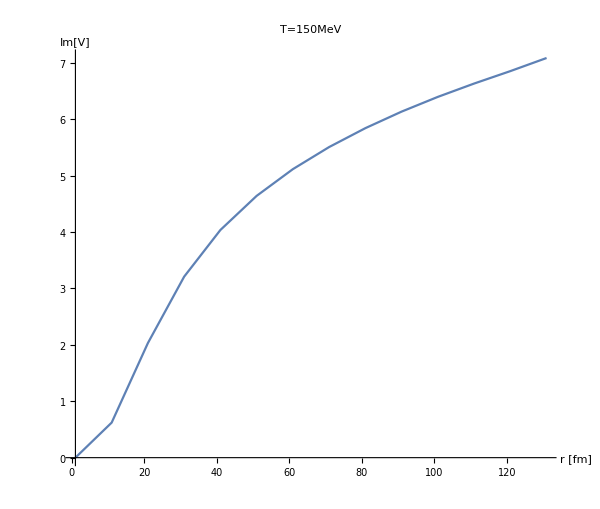

```mathematica
Block[{mD=mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]]},Show[DiscretePlot[ImVs[r,mD,σcont[[1]],0.155],{r,1,140,10},Joined->True,Filling->None,AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},PlotRange->All,AspectRatio->0.85,AxesLabel->{"r [fm]","Im[V]"},PlotLabel->Style["T=150MeV",FontSize->25,FontFamily->"Helvetica",Black],ImageSize->{600,600}]]]
```

```mathematica
ImVs[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

1.42983969503947×10^1794

```mathematica
ImVsS[20000,mDcal[2π,0.155,kfinal[[1]],kfinal[[2]]],σcont[[1]],0.155]
```

19.3738+0. ⅈ

```mathematica
swaveccspectrawsb[T1_]:=Block[{T=T1,mD=mDcalmu[T1,0,kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+15,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+15,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectra/swccT"<>ToString[Round[1000 T]]<>"uspectra.dat",Sort[ccss]];
];
```

```mathematica
swavebbspectrawsb[T1_]:=Block[{T=T1,mD=mDcalmu[T1,0,kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+15,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+15,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectra/swbbT"<>ToString[Round[1000 T]]<>"spectra.dat",Sort[ccss]];
];
```

```mathematica
pwavebbspectrawsb[T1_]:=Block[{T=T1,mD=mDcalmu[T1,0,kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+15,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+15,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectra/pwbbT"<>ToString[Round[1000 T]]<>"lspectra.dat",Sort[ccss]];
];
```

```mathematica
pwaveccspectrawsb[T1_]:=Block[{T=T1,mD=mDcalmu[T1,0,kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V},

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,1/1000,10,1/100}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,101/10,25,1/10}],ParallelTable[{r,ImV[r,mD,α,σ,T]},{r,26,140,1}],ParallelTable[{r,ImVc[r,mD,α,T]+ImVsS[r+15,mD,σ,T]},{r,141,1500,1}],ParallelTable[{r,ImVc[r+15,mD,α,T]+ImVsS[r,mD,σ,T]},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["spectra/pwccT"<>ToString[Round[1000 T]]<>"lspectra.dat",Sort[ccss]];
];
```

### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
pwaveccspectrawsb[0.155]
```

```mathematica
swaveccspectrawsb[0.155]//AbsoluteTiming
```

{2671.83,Null}

```mathematica
swavebbspectrawsb[0.155]//AbsoluteTiming
```

{366.615,Null}

```mathematica
swavebbspectrawsb[0.155]//AbsoluteTiming
```

{231.128,Null}

```mathematica
pwavebbspectrawsb[0.155]//AbsoluteTiming
```

{492.783,Null}

```mathematica
pwavebbspectrawsb[0.155]//AbsoluteTiming
```

{863.201,Null}

```mathematica
Do[swaveccuspectra[i,Tmuscan],{i,Length[Tmuscan]}]//AbsoluteTiming
```

```mathematica
Do[swavecclspectra[i,Tmuscan],{i,Length[Tmuscan]}]//AbsoluteTiming
```